```mathematica
λ=0.1 10^-6;
objectfunction[{x1_,x2_,x3_},{v1_,v2_,v3_},{d1_,d2_,d3_}]:=
Block[{xi=d1/3},
v1 Boole[x1^2+x2^2+x3^2≤ d1^2]
+(v2-v1) Boole[x1^2+x2^2+x3^2-2xi(x1+x2+x3)+3xi^2≤ d2^2]
+(v3-v1) Boole[x1^2+x2^2+x3^2+2xi(x1+x2+x3)+3xi^2≤ d3^2]
]
```

Coordinate are measured in microns. The values of the object function are in the range of the value for polystyrene.

```mathematica
objectsizeradius=108/2;
object[x_]:=objectfunction[x,{- 5 10^-7,- 10.5 10^-7,-2 10^-7},{objectsizeradius,18,18}];
```

```mathematica
Block[{nop=32,d=objectsizeradius,t},
Print[
TableForm[{{"Sample Points:",nop,
"Total time:",
t=Timing[list=Table[downstream[x,y,.3],{x,-d,d,2d/nop},{y,-d,d,2d/nop}]
][[1]]/60,
"min,  time per sample point:",
60t/nop/nop
}}]
];
]
```

Total time: | 3.58969 | min,  time per sample point: | 0.841334

```mathematica
Block[{nop=64,d=objectsizeradius,ob,t,theta=.3,sub,xint},

sub=If[theta≠π/2,xint=x2;Solve[x-x1 Cos[theta]-x2 Sin[theta]==0,x1],xint=x1;Solve[x-x1 Cos[theta]-x2 Sin[theta]==0,x2]][[1]];

ob=Evaluate@object[{x1,x2,y}]/.sub;




(*Print[
TableForm[{{"Sample Points:",nop,
"Total time:",
t=Timing[list2=Chop@Table[ 

Exp[ⅈ 2π/λ 
Integrate[
ob ,{xint,-objectsizeradius,objectsizeradius}
]
]

,{x,-d,d,2d/nop},{y,-d,d,2d/nop}]
][[1]]/60,
"min,  time per sample point:",
60t/nop/nop
}}]
];*)
]
```

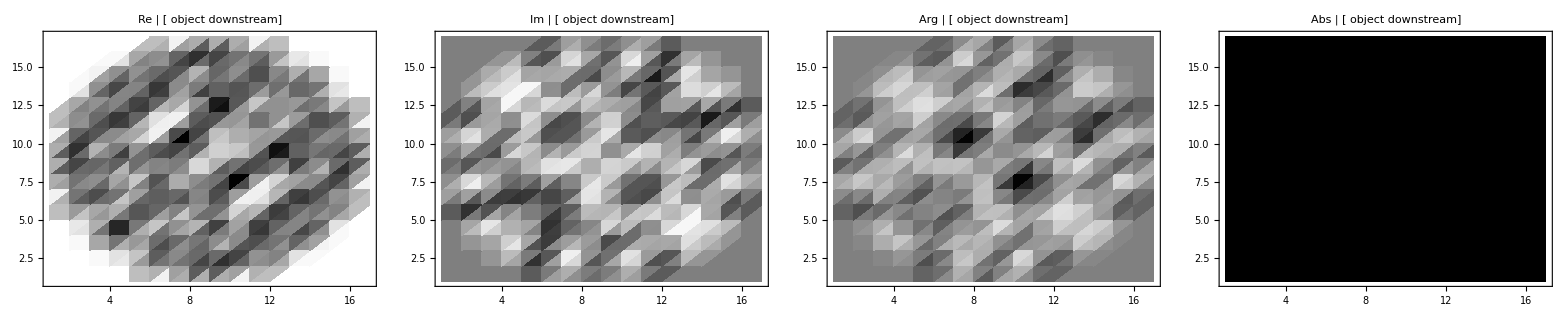

```mathematica
TableForm@{Table[ListDensityPlot[what@list,ColorFunction->GrayLevel,PlotLabel->TableForm[{{what,"[ object downstream]"}}]],{what,{Re,Im,Arg,Abs}}]}
```

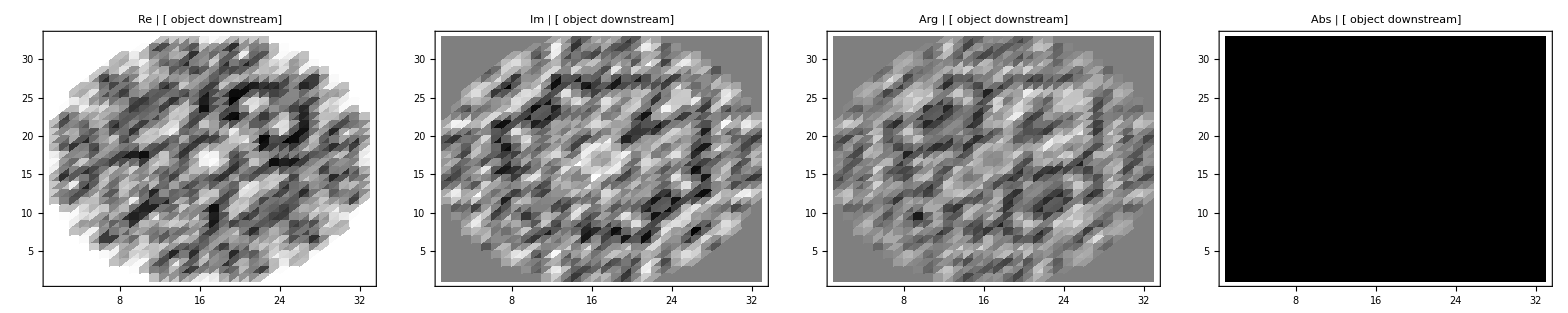

```mathematica
TableForm@{Table[ListDensityPlot[what@list2,ColorFunction->GrayLevel,PlotLabel->TableForm[{{what,"[ object downstream]"}}]],{what,{Re,Im,Arg,Abs}}]}
```